# 1D linear stability analysis (LSA) phase diagrams for the PAR models

This file reuses the same core solver as the E. coli MinDE model. The state variables therefore retain their Min-system names and are reinterpreted as the corresponding PAR quantities according to the mapping below.
Species correspondence:
       MinD  ->  aPAR   (anterior PAR proteins)
       MinE  ->  pPAR   (posterior PAR proteins)
Unlike MinD, the PAR proteins carry no nucleotide (ATP/ADP) cycle, so the ADP-bound cytosolic state has no counterpart in the PAR model.
Variable mapping (Min name -> PAR meaning):
       cDT  ->  cytosolic aPAR
       cDD  ->  (unused; no ADP-bound cytosolic state in the PAR system)
       cE   ->  cytosolic pPAR
       md   ->  membrane-bound aPAR
       mde  ->  membrane-bound pPAR
All remaining symbols (rate constants, diffusion coefficients, geometry, ...) keep their Min-system names; their values are set to the PAR parameters in the configuration section below.

```mathematica
paramsSkeletonScaled={
rhoD->2,
rhoE->1.4,
DD->1.5,
DE->1.5,
Dd->0.28,
Dde->1,
konA->0.1,
koffA->5.4*10^-3,
konP->1,
koffP->7.3*10^-3,
kAP->0.190,
kPA->2.0,
α->1,
β->2
};
```

## Setup

Setup the reaction terms.

```mathematica
f={0,
-(konA cDT -koffA md -kAP md mde^α),(*Ac*)
-(konP cE -koffP mde-kPA mde md^β),(*Pc*)
konA cDT -koffA md -kAP md mde^α,(*Am*)
konP cE -koffP mde-kPA mde md^β(*Pm*)
};
```

Conservation laws:

```mathematica
Simplify@Total@f[[{1,2,4}]]
Simplify[Total@f[[{3,5}]]]
```

0

0

## Homogeneous fixed point(s)

```mathematica
ClearAll@hss;
hss[params_]:=Block[{sol},
sol=NSolve[{0==f,rhoD==cDT+md,rhoE==cE+mde,cDD==0}/.params,{cDD,cDT,cE,md,mde}];
Select[{cDD,cDT,cE,md,mde}/.sol,AllTrue[#,NonNegative]&]
];
```

```mathematica
hss[paramsSkeletonScaled]
```

{{0.,0.91785,0.982014,1.08215,0.417986}}

## LSA

```mathematica
eqs={-DD q^2cDD,
-DD q^2cDT,
-DE q^2cE,
-Dd q^2 md,
-Dde q^2 mde}+f;
```

```mathematica
jac=D[eqs,{{cDD,cDT,cE,md,mde}}];
```

```mathematica
ClearAll@dispersionRelation;
Options[dispersionRelation]={"gpts"->100,"maxQ"->5};
dispersionRelation[params_,opts:OptionsPattern[]]:=Block[{gpts=OptionValue["gpts"],Q=OptionValue["maxQ"],HSS=hss[params],JAC},
JAC=(jac/.Thread[{cDD,cDT,cE,md,mde}->#]/.params)&/@HSS;
{
Function[jj,{#,SortBy[Eigenvalues[jj/.q->#],Re[#]&]}&/@(Q Range[0,1,1/gpts])]/@JAC,
HSS
}
];
```

### Type-of-instability test

```mathematica
ClearAll@testInstab;
Options[testInstab]={"gpts"->100,"maxQ"->5};
testInstab[params_?(AllTrue[#,Function[x,NonNegative[x[[2]]]]]&),opts:OptionsPattern[]]:=Block[{
dispRel=dispersionRelation[params,"gpts"->OptionValue["gpts"],"maxQ"->OptionValue["maxQ"]],
HSS,
hssInd,
hssTypes,
hssLS,
sigma0,
qNZero,sigmaNZero,
sigmac,qc,
zero (*test whether there the dispersion relation is below 0 at q<qc*)
},
(*find laterally-unstable HSS*)
If[Length[dispRel[[1]]]==1,

HSS=dispRel[[2,1]];
dispRel=dispRel[[1,1]];
hssTypes=1;,(*just one steady state*)

(*locally stable hss*)
hssLS=Select[Range[Length[dispRel[[1]]]],Re[dispRel[[1,#,1,2,-1]]]< 10^-10&];

(*classify the hss's*)
If[Length[dispRel[[1]]]==2,
If[Length[hssLS]==0,
hssTypes=4;,(*two hss, both locally unstable*)
If[Length[hssLS]==1,
hssTypes=2;,(*two hss, one locally stable*)
hssTypes=3;];(*two hss, both locally stable*)
];,
If[Length[dispRel[[1]]]==3,
hssTypes=5;,(*three hss*)
hssTypes=6;];(*more than three hss*)
];

(*select the Turing-unstable hss, otherwise the most unstable hss*)
If[Length[hssLS]>0,
hssInd=Last@SortBy[hssLS,Max@Re[dispRel[[1,#,All,2,-1]]]&];
If[Max@Re[dispRel[[1,hssInd,All,2,-1]]]>0,
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];,
hssInd=Last@SortBy[Range[Length[dispRel[[1]]]],Max@Re[dispRel[[1,#,All,2,-1]]]&];
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];
];,
hssInd=Last@SortBy[Range[Length[dispRel[[1]]]],Max@Re[dispRel[[1,#,All,2,-1]]]&];
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];
];

];


sigma0=dispRel[[1,2,-1]];
qNZero=Min[Select[dispRel[[2;;]],Re@#[[2,-1]]<0&][[All,1]]];
If[qNZero==Infinity,
sigmaNZero=-1;,
sigmaNZero=SortBy[Select[dispRel,#[[1]]≥qNZero&],Re@#[[2,-1]]&][[-1,2,-1]];
];
{qc,sigmac}={#[[1]],#[[2,-1]]}&@First@Select[dispRel,Max[Re@dispRel[[All,2,-1]]]==Re@#[[2,-1]]&];
zero=If[qNZero<qc,1,0];
{
If[Re[sigma0]>10^-8,
If[qc==0,
If[Re@sigmaNZero>0,
2,(*type-III + type-I instability with sigma<0 in between*)
1],(*type-III instability*)
If[1==zero,
4,(*type-I + type-III instability with sigma<0 in between*)
3](*type-I + type-III instability with sigma>0 in between*)
],
If[qc==0,
0,(*no instability*)
If[1==zero,
5,(*type-I instability*)
6 ](*type-II instability*)
]
],
dispRel,
hssTypes,
HSS,
sigmac
}
];
```

### Dispersion-relation approximation

```mathematica
ClearAll@predDisp;
predDisp[params_?(AllTrue[#,Function[x,NonNegative[x[[2]]]]]&)]:=Block[{
HSS=testInstab[params][[-2]],
JAC,
nv,
vecD,
vecE,
dispRelPred,
qMin,qMax,
qss,loc},
(*The nullcline tangent vectors lie in the nullspace of the Jacobian of the reaction terms*)
JAC=jac/.Thread[{cDD,cDT,cE,md,mde}->HSS]/.params/.q->0;
nv=NullSpace[JAC];
(*Find the vectors in the nullspace that only vary total MinD (vecD) or total MinE (vecE) concentration, respectively*)
vecD=#/({0,1,0,1,0}.#)&@((a nv[[1]]+b nv[[2]])/.First@Solve[{{0,0,1,0,1}.(a nv[[1]]+b nv[[2]])==0,a+b==1},{a,b}]);
vecE=#/({0,0,1,0,1}.#)&@((a nv[[1]]+b nv[[2]])/.First@Solve[{{0,1,0,1,0}.(a nv[[1]]+b nv[[2]])==0,a+b==1},{a,b}]);
(*Approximation of the leading two eigenvalues of the dispersion relation*)
dispRelPred=Eigenvalues[{{DD vecD[[2]]+DD/(1+DD/λ q^2)vecD[[1]]+Dd vecD[[4]],DD vecE[[2]]+DD/(1+DD/λ q^2)vecE[[1]]+Dd vecE[[4]]},
{DE vecD[[3]]+Dde vecD[[5]],DE vecE[[3]]+Dde vecE[[5]]}}]/.params;
(*Find the zero crossing of the dispersion relation (real part) or return 0 if not existent*)
qMin=Quiet[Check[Abs@(q/.FindRoot[Re@#==0,{q,0.1}]),0]]&/@dispRelPred;
(*qss approximation of the dispersion relation*)
qss=Min@Re[Eigenvalues[{{DD vecD[[2]]+DD vecD[[1]]+Dd vecD[[4]],DD vecE[[2]]+DD vecE[[1]]+Dd vecE[[4]]},
{DE vecD[[3]]+Dde vecD[[5]],DE vecE[[3]]+Dde vecE[[5]]}}]/.params];
loc=Chop@Max@Re[Eigenvalues[JAC]];
{-q^2 dispRelPred,qMin,qss,loc}
]
```

```mathematica
ClearAll@predSlopes;
predSlopes[params_?(AllTrue[#,Function[x,NonNegative[x[[2]]]]]&)]:=Block[{
HSS=testInstab[params][[-2]],
JAC,
nv,
vecD,
vecE,
slopeEtaD,
slopeEtaE},
(*The nullcline tangent vectors lie in the nullspace of the Jacobian of the reaction terms*)
JAC=jac/.Thread[{cDD,cDT,cE,md,mde}->HSS]/.params/.q->0;
nv=NullSpace[JAC];
(*Find the vectors in the nullspace that only vary total MinD (vecD) or total MinE (vecE) concentration, respectively*)
vecD=#/({0,1,0,1,0}.#)&@((a nv[[1]]+b nv[[2]])/.First@Solve[{{0,0,1,0,1}.(a nv[[1]]+b nv[[2]])==0,a+b==1},{a,b}]);
vecE=#/({0,0,1,0,1}.#)&@((a nv[[1]]+b nv[[2]])/.First@Solve[{{0,1,0,1,0}.(a nv[[1]]+b nv[[2]])==0,a+b==1},{a,b}]);
slopeEtaD=DD vecD[[2]]+Dd vecD[[4]]/.params;
slopeEtaE=DD vecE[[3]]+Dde vecE[[5]]/.params;
{slopeEtaD,slopeEtaE}
]
```

```mathematica
ClearAll@predSlopescross;
predSlopescross[params_?(AllTrue[#,Function[x,NonNegative[x[[2]]]]]&)]:=Block[{
HSS=testInstab[params][[-2]],
JAC,
nv,
vecD,
vecE,
ad,
bc},
(*The nullcline tangent vectors lie in the nullspace of the Jacobian of the reaction terms*)
JAC=jac/.Thread[{cDD,cDT,cE,md,mde}->HSS]/.params/.q->0;
nv=NullSpace[JAC];
(*Find the vectors in the nullspace that only vary total MinD (vecD) or total MinE (vecE) concentration, respectively*)
vecD=#/({0,1,0,1,0}.#)&@((a nv[[1]]+b nv[[2]])/.First@Solve[{{0,0,1,0,1}.(a nv[[1]]+b nv[[2]])==0,a+b==1},{a,b}]);
vecE=#/({0,0,1,0,1}.#)&@((a nv[[1]]+b nv[[2]])/.First@Solve[{{0,1,0,1,0}.(a nv[[1]]+b nv[[2]])==0,a+b==1},{a,b}]);
ad=(DD vecD[[2]]+Dd vecD[[4]])(DD vecE[[3]]+Dde vecE[[5]])/.params;
bc=(DD vecD[[3]]+Dde vecD[[5]])(DD vecE[[2]]+Dd vecE[[4]])/.params;
{bc-ad}
]
```

## LSA

### Vary konA, konP

```mathematica
Monitor[sweepLSA=Table[
{
vps,
testInstab[Join[{konA->vps[[1]],konP->vps[[2]]},DeleteCases[paramsSkeletonScaled,(konA->_)|(konP->_)]],"gpts"->100]
},{vps,Flatten[Outer[List,10^Range[-1.5,-0.5,0.05],10^Range[-0.5,0.5,0.05]],1]}];,vps]
```

```mathematica
Monitor[sweepLSASlopes=Table[
{
vps,
predSlopes[Join[{konA->vps[[1]],konP->vps[[2]]},DeleteCases[paramsSkeletonScaled,(konA->_)|(konP->_)]]]
},{vps,Flatten[Outer[List,10^Range[-1.5,-0.5,0.05],10^Range[-0.5,0.5,0.05]],1]}];,vps]
```

```mathematica
Monitor[sweepLSASlopescross=Table[
{
vps,
predSlopescross[Join[{konA->vps[[1]],konP->vps[[2]]},DeleteCases[paramsSkeletonScaled,(konA->_)|(konP->_)]]]
},{vps,Flatten[Outer[List,10^Range[-1.5,-0.5,0.05],10^Range[-0.5,0.5,0.05]],1]}];,vps]
```

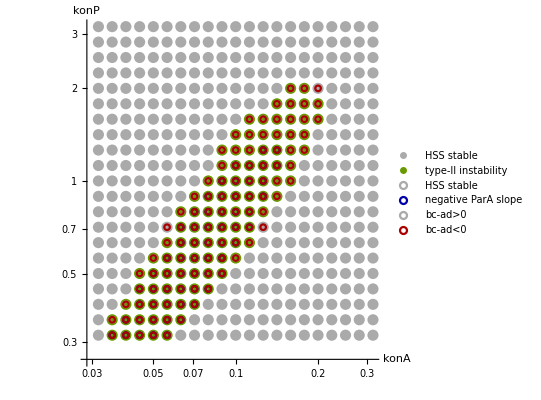

```mathematica
Show[
ListLogLogPlot[DeleteCases[{
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA,#[[2,1]]==0&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA,#[[2,1]]==1&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA,#[[2,1]]==2&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA,#[[2,1]]==3&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA,#[[2,1]]==4&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA,#[[2,1]]==5&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA,#[[2,1]]==6&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA,#[[2,1]]==5&&Im@#[[2,-1]]!=0&]
},
{}],PlotStyle->({#,PointSize[0.02]}&/@Join[{Lighter@Gray},ColorData[90,"ColorList"]]),AxesLabel->(Style[#,FontSize->14]&/@{"konA","konP"}),
TicksStyle->Directive[14],AspectRatio->1,
AxesStyle->Thickness[0.002],PlotLegends->((
#[[1]]&/@DeleteCases[{#[[2,1]]&/@Select[sweepLSA,#[[2,1]]==0&],
#[[2,1]]&/@Select[sweepLSA,#[[2,1]]==1&],
#[[2,1]]&/@Select[sweepLSA,#[[2,1]]==2&],
#[[2,1]]&/@Select[sweepLSA,#[[2,1]]==3&],
#[[2,1]]&/@Select[sweepLSA,#[[2,1]]==4&],
#[[2,1]]&/@Select[sweepLSA,#[[2,1]]==5&],
#[[2,1]]&/@Select[sweepLSA,#[[2,1]]==6&],
7&/@Select[sweepLSA,#[[2,1]]==5&&Im@#[[2,-1]]!=0&]},{}])/.{0->"HSS stable",1->"type-III instability",2->"type-III + type-I instability with σ<0 in between",3->"type-I + type-III instability with σ>0 for q<qc",4->"type-I + type-III instability with σ<0 for q<qc",5->"type-I instability",6->"type-II instability",7->"oscillatory type-I instability"})],
ListLogLogPlot[DeleteCases[{
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASlopes,(#[[2,1]]>0)&&(#[[2,2]]>0)&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASlopes,(#[[2,1]]<0)&&(#[[2,2]]>0)&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASlopes,(#[[2,1]]>0)&&(#[[2,2]]<0)&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASlopes,(#[[2,1]]<0)&&(#[[2,2]]<0)&]
},{}],PlotMarkers->({Graphics[{#,Circle[]}],0.03}&/@{Lighter@Gray,Darker@Blue,(*Lighter@Blue,*)Darker@Red,Black}),PlotLegends->{"HSS stable","negative ParA slope","negative ParP slope","negative both slope"}],
ListLogLogPlot[DeleteCases[{
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASlopescross,(#[[2,1]]<0)&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASlopescross,(#[[2,1]]>0)&]
},{}],PlotMarkers->({Graphics[{#,Circle[]}],0.04}&/@{Lighter@Gray,Darker@Red}),PlotLegends->{"bc-ad>0","bc-ad<0"}]
]
```

## Making the region from only the concentration

```mathematica
(*setting up grids*)
numberofpoints=50;
xstest=Flatten@Table[a,{a,0,3,0.2},{b,0,3,0.2}];
ystest=Flatten@Table[b,{a,0,3,0.2},{b,0,3,0.2}];

(*LSA*)
Monitor[sweepLSAnoLog=Table[
{
vps,
testInstab[Join[{rhoD->vps[[1]],rhoE->vps[[2]]},DeleteCases[paramsSkeletonScaled,(rhoD->_)|(rhoE->_)]],"gpts"->100]
},{vps,Flatten[Outer[List,Range[0.2,3,0.2],Range[0.2,3,0.2]],1]}];,vps]
```

#### Generating Homogenous steady state concentrations

```mathematica
xs=xstest;
ys=ystest;
Monitor[sweepConcA=Table[

hss[Join[{rhoD->xs[[aa]],rhoE->ys[[aa]]},DeleteCases[paramsSkeletonScaled,(rhoD->_)|(rhoE->_)]]][[1]][[2]]
,{aa,1,Length[xs],1}];,aa]
Monitor[sweepConcP=Table[

hss[Join[{rhoD->xs[[aa]],rhoE->ys[[aa]]},DeleteCases[paramsSkeletonScaled,(rhoD->_)|(rhoE->_)]]][[1]][[3]]
,{aa,1,Length[xs],1}];,aa]
Monitor[sweepConmA=Table[

hss[Join[{rhoD->xs[[aa]],rhoE->ys[[aa]]},DeleteCases[paramsSkeletonScaled,(rhoD->_)|(rhoE->_)]]][[1]][[4]]
,{aa,1,Length[xs],1}];,aa]
Monitor[sweepConmP=Table[

hss[Join[{rhoD->xs[[aa]],rhoE->ys[[aa]]},DeleteCases[paramsSkeletonScaled,(rhoD->_)|(rhoE->_)]]][[1]][[5]]
,{aa,1,Length[xs],1}];,aa]

(* hss are then analysed in Python file "Multi-component_classification_PAR.ipynb" *)
```

```mathematica
(* Reset input from Python *)
SlopeFromPython={False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True};
pointsTrue=Pick[Transpose[{xstest,ystest}],SlopeFromPython,True];
pointsFalse=Pick[Transpose[{xstest,ystest}],SlopeFromPython,False];
```

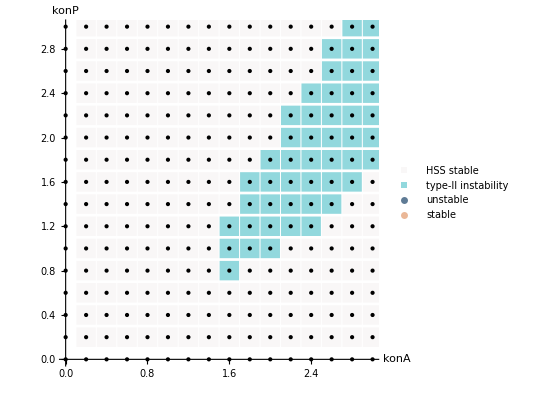

```mathematica
Show[ListPlot[DeleteCases[{
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSAnoLog,#[[2,1]]==0&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSAnoLog,#[[2,1]]==1&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSAnoLog,#[[2,1]]==2&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSAnoLog,#[[2,1]]==3&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSAnoLog,#[[2,1]]==4&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSAnoLog,#[[2,1]]==5&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSAnoLog,#[[2,1]]==6&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSAnoLog,#[[2,1]]==5&&Im@#[[2,-1]]!=0&]
},
{}],PlotStyle->({#,PointSize[10]}&/@Join[{RGBColor[0.975,0.969,0.969]},{RGBColor[0.574,0.847,0.868]}]),PlotRange->{{0,3},{0,3}},AxesLabel->(Style[#,FontSize->14]&/@{"konA","konP"}),
PlotMarkers->{Graphics[{EdgeForm[],Rectangle[{-.5,-.5},{.5,.5}]}],20},
TicksStyle->Directive[14],AspectRatio->1,
AxesStyle->Thickness[0.002],PlotLegends->((
#[[1]]&/@DeleteCases[{#[[2,1]]&/@Select[sweepLSAnoLog,#[[2,1]]==0&],
#[[2,1]]&/@Select[sweepLSAnoLog,#[[2,1]]==1&],
#[[2,1]]&/@Select[sweepLSAnoLog,#[[2,1]]==2&],
#[[2,1]]&/@Select[sweepLSAnoLog,#[[2,1]]==3&],
#[[2,1]]&/@Select[sweepLSAnoLog,#[[2,1]]==4&],
#[[2,1]]&/@Select[sweepLSAnoLog,#[[2,1]]==5&],
#[[2,1]]&/@Select[sweepLSAnoLog,#[[2,1]]==6&],
7&/@Select[sweepLSAnoLog,#[[2,1]]==5&&Im@#[[2,-1]]!=0&]},{}])/.{0->"HSS stable",1->"type-III instability",2->"type-III + type-I instability with σ<0 in between",3->"type-I + type-III instability with σ>0 for q<qc",4->"type-I + type-III instability with σ<0 for q<qc",5->"type-I instability",6->"type-II instability",7->"oscillatory type-I instability"})],
ListPlot[{Style[pointsTrue,RGBColor[0.373,0.482,0.584]],Style[pointsFalse,RGBColor[0.918,0.718,0.592]]},PlotStyle->{PointSize[0.03],PointSize[0.03]},PlotLegends->{"unstable","stable"},AxesOrigin->{0,0},PlotRange->All,AxesLabel->(Style[#,FontSize->14]&/@{"ρ_A","ρ_P"}),
TicksStyle->Directive[14],AspectRatio->1,
AxesStyle->Thickness[0.002]]]
```

#### Simulation of spatial profiles on a domain with no - flux boundary conditions

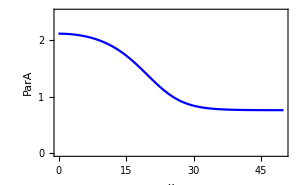
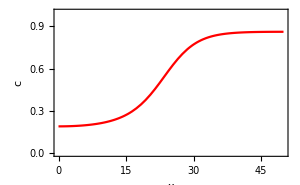

```mathematica
params={
rhoD->2,
rhoE->1.4,
DD->1.5,
DE->1.5,
Dd->0.28,
Dde->1,
konA->10^-0.8,
koffA->5.4*10^-3,
konP->10^0.2,
koffP->7.3*10^-3,
kAP->0.190,
kPA->2.0,
α->1,
β->2,
L->50
};

(* stable set*)
(*
params={
rhoD->2,
rhoE->1.4,
DD->1.5,
DE->1.5,
Dd->0.28,
Dde->1,
konA->10^-0.6,
koffA->5.4*10^-3,
konP->10^-0.3,
koffP->7.3*10^-3,
kAP->0.190,
kPA->2.0,
α->1,
β->2,
L->50
};
*)

(* Setting up random initial concentration profile *)
randomcof=RandomReal[0.2,100]-0.1;
randomfluc=0.001∑_(k=1)^20 randomcof[[k]]*Cos[(π *x*k)/(L/.params)];

(* setting up Reaction-diffusion equations *)
HSS=hss[params];
runTwoComponentSim[{f_},params_,{HSS_,ram_},tMax_]:=First@NDSolve[{
D[cDT[x,t],t]==DD D[cDT[x,t],{x,2}]+(f[[2]]/.{cDD->cDD[x,t],cDT->cDT[x,t],cE->cE[x,t],md->md[x,t],mde->mde[x,t]}),
D[cE[x,t],t]==DE D[cE[x,t],{x,2}]+(f[[3]]/.{cDD->cDD[x,t],cDT->cDT[x,t],cE->cE[x,t],md->md[x,t],mde->mde[x,t]}),
D[md[x,t],t]==Dd D[md[x,t],{x,2}]+(f[[4]]/.{cDD->cDD[x,t],cDT->cDT[x,t],cE->cE[x,t],md->md[x,t],mde->mde[x,t]}),
D[mde[x,t],t]==Dde D[mde[x,t],{x,2}]+(f[[5]]/.{cDD->cDD[x,t],cDT->cDT[x,t],cE->cE[x,t],md->md[x,t],mde->mde[x,t]}),
(D[cDT[x,t],x]/.x->0)==0,
(D[cE[x,t],x]/.x->0)==0,
(D[md[x,t],x]/.x->0)==0,
(D[mde[x,t],x]/.x->0)==0,
(D[cDT[x,t],x]/.x->(L/.params))==0,
(D[cE[x,t],x]/.x->(L/.params))==0,
(D[md[x,t],x]/.x->(L/.params))==0,
(D[mde[x,t],x]/.x->(L/.params))==0,
cDT[x,0]==HSS[[1]][[2]],
cE[x,0]==HSS[[1]][[3]],
md[x,0]==HSS[[1]][[4]]+ram,
mde[x,0]==HSS[[1]][[5]]
}/.params,
{cDT,cE,md,mde},
{x,0,L/.params},{t,0,tMax},
Method-> {"PDEDiscretization"->{
"MethodOfLines",
 "SpatialDiscretization"->{
"TensorProductGrid",
"MinPoints"->500
}
}}
];
testRun=runTwoComponentSim[
{f},(* reaction kinetics *)
params,
{(* initial condition *)
HSS,randomfluc
}/.params,
1000000(* tMax *)
];

outtime=1000000; 
omm1=Plot[Evaluate[md[x,outtime]/.testRun],{x,0,L/.params},
PlotRange->{0,2.5},Axes->False,Frame->{True,True,True,False},ImageSize->300,FrameStyle->Thick,PlotStyle->Blue,
ImagePadding->50,FrameStyle->Thick,FrameLabel->{Style["x",14],Style["ParA",14],Null,Null},FrameTicks->{{{0,1,2},None},{None,None}
},FrameTicksStyle->Directive[Black,14]];
omm2=Plot[Evaluate[mde[x,outtime]/.testRun],{x,0,L/.params},
PlotRange->{0,1},
AxesLabel->{x,c},ImagePadding->50,FrameLabel->{Null,Null,Null,Style["ParP",14]}
,ImageSize->300,PlotStyle->Red,Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,{0,0.5,1}},{None,None}},FrameStyle->Thick,ImageSize->Large,FrameTicksStyle->Directive[Black,14]];

Overlay[{omm1,omm2}]
```